```mathematica
ClearAll["Global`*"];

(* =========================================*)
(*PHASE 2:NATIVE MATHEMATICA Hg CALIBRATION*)
(*Main-report numerical analysis*)
(* =========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hgDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hg_calibration"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

fitDir=FileNameJoin[{outRoot,"Hg_native_fit_reports"}];
calDir=FileNameJoin[{outRoot,"Calibration_outputs"}];

CreateDirectory[fitDir];
CreateDirectory[calDir];

Print["Output folder: ",outRoot];


(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",hgDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

fmt[x_]:=ToString[NumberForm[N[x],{Infinity,6},NumberPoint->"."]];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];


(*----------Hg specs----------*)
(*Use 365.588,404.770,546.226 as main calibration points.The 365.119 scan is saved as diagnostic only because it appears crowded/ambiguous.The repeated 546 scans are repeatability checks,not independent calibration lines.*)

hgSpecs={<|"id"->"Hg 365.119 diagnostic","fileKey"->"365.12","trueWL"->365.119,"window"->{365.50,365.85},"useForCalibration"->False|>,<|"id"->"Hg 365.588","fileKey"->"365.588","trueWL"->365.588,"window"->{365.50,365.90},"useForCalibration"->True|>,<|"id"->"Hg 404.770","fileKey"->"404.770","trueWL"->404.770,"window"->{405.05,405.42},"useForCalibration"->True|>,<|"id"->"Hg 546.226","fileKey"->"546.226","trueWL"->546.226,"window"->{546.50,546.92},"useForCalibration"->True|>,<|"id"->"Hg 546 repeat wide","fileKey"->"562hg_2nm_scan","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>,<|"id"->"Hg 546 repeat 20um","fileKey"->"same_data","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>};


(*----------fit one peak----------*)

fitOneHg[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,c0,d0,amp0,mu0,sig0,x0,edgeN,fit,params,errs,resid,rms,maxresid,fitPlot,residPlot,table,report,outFile,c,d,amp,mu,sig,x},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["id"]];
Return[<|"id"->spec["id"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<8,Print["Too few points for ",spec["id"]];
Return[<|"id"->spec["id"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
	c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
amp0=Max[yvals]-c0;
mu0=xvals[[First@Ordering[yvals,-1]]];
sig0=(xmax-xmin)/6;
fit=Quiet@NonlinearModelFit[data,c+d (x-x0)+amp Exp[-(x-mu)^2/(2 sig^2)],{{c,c0},{d,d0},{amp,amp0},{mu,mu0},{sig,sig0}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
errs=fit["ParameterErrors"];
resid=data/. {xx_,yy_}:>{xx,yy-fit[xx]};
rms=Sqrt[Mean[resid[[All,2]]^2]];
maxresid=Max[Abs[resid[[All,2]]]];
fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,8},PlotRange->All,ImageSize->750,FrameLabel->{"Wavelength (nm)","Signal (V)"},PlotLabel->Style[spec["id"]<>": Gaussian + linear background",14,Black]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}]];
residPlot=ListPlot[resid,Frame->True,Axes->False,PlotMarkers->{Automatic,8},PlotRange->All,ImageSize->750,FrameLabel->{"Wavelength (nm)","Residual (V)"},PlotLabel->Style["Residuals",13,Black],GridLines->{None,{0}}];
table=Grid[{{"parameter","estimate","standard error"},{"c",c/. params,errs[[1]]},{"d",d/. params,errs[[2]]},{"amp",amp/. params,errs[[3]]},{"mu",mu/. params,errs[[4]]},{"sigma",sig/. params,errs[[5]]},{"RMS residual",rms,""},{"max |residual|",maxresid,""},{"true Hg wavelength",spec["trueWL"],""},{"used for calibration?",spec["useForCalibration"],""}},Frame->All,Alignment->Left];
report=Column[{Style["Native Mathematica fit report: "<>spec["id"],16,Bold],Style["File: "<>FileNameTake[file],10],Style["Fit window: "<>ToString[spec["window"]]<>" nm",10],fitPlot,residPlot,table},Spacings->1];
outFile=FileNameJoin[{fitDir,makeName[spec["id"]]<>"_native_fit_report.pdf"}];
Export[outFile,report,"PDF"];
<|"id"->spec["id"],"status"->"fit_complete","file"->FileNameTake[file],"trueWL_nm"->spec["trueWL"],"fit_xmin_nm"->xmin,"fit_xmax_nm"->xmax,"n_points"->Length[data],"mu_obs_nm"->(mu/. params),"mu_SE_nm"->errs[[4]],"sigma_nm"->(sig/. params),"sigma_SE_nm"->errs[[5]],"amp"->(amp/. params),"amp_SE"->errs[[3]],"background_c"->(c/. params),"background_d"->(d/. params),"rms_residual"->rms,"max_abs_residual"->maxresid,"useForCalibration"->spec["useForCalibration"],"report_pdf"->outFile|>];


(*----------run fits----------*)

results=fitOneHg/@hgSpecs;

Export[FileNameJoin[{outRoot,"Hg_native_peak_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

Dataset[results]


(*----------calibration fit----------*)

calRows=Select[results,#["status"]=="fit_complete"&&TrueQ[#["useForCalibration"]]&];

calData=({#["mu_obs_nm"],#["trueWL_nm"]}&/@calRows);

linCal=LinearModelFit[calData,{1,x},x];

calParams=linCal["BestFitParameters"];
calErrors=linCal["ParameterErrors"];

a=calParams[[1]];
b=calParams[[2]];

sigmaA=calErrors[[1]];
sigmaB=calErrors[[2]];

calResiduals=calData/. {xo_,yt_}:>{xo,yt-linCal[xo]};
resVals=calResiduals[[All,2]];

rmsCal=Sqrt[Mean[resVals^2]];
maxCal=Max[Abs[resVals]];

calSummary={{"quantity","value"},{"a_intercept_nm",a},{"sigma_a_nm",sigmaA},{"b_slope",b},{"sigma_b",sigmaB},{"RMS_residual_nm",rmsCal},{"max_abs_residual_nm",maxCal}};

Export[FileNameJoin[{calDir,"Hg_linear_calibration_summary.csv"}],calSummary,"CSV"];

Export[FileNameJoin[{calDir,"Hg_calibration_points.csv"}],Prepend[calData,{"observed_mu_nm","true_vacuum_wavelength_nm"}],"CSV"];

Export[FileNameJoin[{calDir,"Hg_linear_calibration_residuals.csv"}],Prepend[calResiduals,{"observed_mu_nm","true_minus_fit_nm"}],"CSV"];

calPlot=Show[ListPlot[calData,Frame->True,Axes->False,PlotMarkers->{Automatic,10},ImageSize->800,FrameLabel->{"Observed Hg center (nm)","True Hg vacuum wavelength (nm)"},PlotLabel->Style["Hg calibration: true wavelength vs observed center",14,Black]],Plot[linCal[x],{x,Min[calData[[All,1]]]-0.5,Max[calData[[All,1]]]+0.5},PlotStyle->{Red,Thick}]];

residPlot=ListPlot[calResiduals,Frame->True,Axes->False,PlotMarkers->{Automatic,10},ImageSize->800,FrameLabel->{"Observed Hg center (nm)","Residual true - fit (nm)"},PlotLabel->Style["Hg calibration residuals",14,Black],GridLines->{None,{0}}];

Export[FileNameJoin[{calDir,"Hg_linear_calibration_plot.pdf"}],calPlot,"PDF"];
Export[FileNameJoin[{calDir,"Hg_linear_calibration_residuals.pdf"}],residPlot,"PDF"];

Print["Linear calibration:"];
Print["lambda_true = a + b lambda_obs"];
Print["a = ",a," ± ",sigmaA];
Print["b = ",b," ± ",sigmaB];
Print["RMS residual = ",rmsCal," nm"];
Print["Max abs residual = ",maxCal," nm"];

Print["DONE. Open output folder:"];
Print[outRoot];

SystemOpen[outRoot];
```

Output folder: C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_native

Linear calibration:

lambda_true = a + b lambda_obs

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

RMS residual = 0.128662 nm

Max abs residual = 0.173043 nm

DONE. Open output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_native

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*CLEAN PHASE 2 Hg OUTPUTS:NO TABLES IN PDF*)
(*Tables saved separately for LaTeX*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hgDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hg_calibration"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

fitFigDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];
calFigDir=FileNameJoin[{outRoot,"compact_calibration_figures"}];

CreateDirectory/@{fitFigDir,tableDir,calFigDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",hgDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

hgSpecs={<|"id"->"Hg 365.119 diagnostic","fileKey"->"365.12","trueWL"->365.119,"window"->{365.50,365.85},"useForCalibration"->False|>,<|"id"->"Hg 365.588","fileKey"->"365.588","trueWL"->365.588,"window"->{365.50,365.90},"useForCalibration"->True|>,<|"id"->"Hg 404.770","fileKey"->"404.770","trueWL"->404.770,"window"->{405.05,405.42},"useForCalibration"->True|>,<|"id"->"Hg 546.226","fileKey"->"546.226","trueWL"->546.226,"window"->{546.50,546.92},"useForCalibration"->True|>,<|"id"->"Hg 546 repeat wide","fileKey"->"562hg_2nm_scan","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>,<|"id"->"Hg 546 repeat 20um","fileKey"->"same_data","trueWL"->546.226,"window"->{546.55,546.90},"useForCalibration"->False|>};

fitOneHgClean[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,edgeN,c0,d0,amp0,mu0,sig0,x0,fit,params,errs,resid,rms,maxresid,fitPlot,residPlot,combinedFig,outFile,c,d,amp,mu,sig,x},file=findFile[spec["fileKey"]];
If[MissingQ[file],Return[<|"id"->spec["id"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<8,Return[<|"id"->spec["id"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
amp0=Max[yvals]-c0;
mu0=xvals[[First@Ordering[yvals,-1]]];
sig0=(xmax-xmin)/6;
fit=Quiet@NonlinearModelFit[data,c+d (x-x0)+amp Exp[-(x-mu)^2/(2 sig^2)],{{c,c0},{d,d0},{amp,amp0},{mu,mu0},{sig,sig0}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
errs=fit["ParameterErrors"];
resid=data/. {xx_,yy_}:>{xx,yy-fit[xx]};
rms=Sqrt[Mean[resid[[All,2]]^2]];
maxresid=Max[Abs[resid[[All,2]]]];
fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[spec["id"],11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}]];
residPlot=ListPlot[resid,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
combinedFig=GraphicsColumn[{fitPlot,residPlot},Spacings->0.15,ImageSize->430];
outFile=FileNameJoin[{fitFigDir,makeName[spec["id"]]<>"_fit_residual_clean.pdf"}];
Export[outFile,combinedFig,"PDF"];
<|"id"->spec["id"],"status"->"fit_complete","trueWL_nm"->spec["trueWL"],"mu_obs_nm"->(mu/. params),"mu_SE_nm"->errs[[4]],"sigma_nm"->(sig/. params),"sigma_SE_nm"->errs[[5]],"amp"->(amp/. params),"amp_SE"->errs[[3]],"background_c"->(c/. params),"background_d"->(d/. params),"rms_residual"->rms,"max_abs_residual"->maxresid,"useForCalibration"->spec["useForCalibration"],"figure_pdf"->outFile|>];

results=fitOneHgClean/@hgSpecs;

Export[FileNameJoin[{tableDir,"Hg_native_peak_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

(*Optional LaTeX-ready table body*)
latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["id"],NumberForm[r["trueWL_nm"],{8,3}],NumberForm[r["mu_obs_nm"],{8,3}],NumberForm[r["mu_SE_nm"],{8,5}],NumberForm[r["sigma_nm"],{8,4}],NumberForm[r["rms_residual"],{8,4}],r["useForCalibration"]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"Hg_native_peak_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*Calibration using selected rows*)
calRows=Select[results,#["status"]=="fit_complete"&&TrueQ[#["useForCalibration"]]&];

calData=({#["mu_obs_nm"],#["trueWL_nm"]}&/@calRows);

linCal=LinearModelFit[calData,{1,x},x];

calParams=linCal["BestFitParameters"];
calErrors=linCal["ParameterErrors"];

a=calParams[[1]];
b=calParams[[2]];
sigmaA=calErrors[[1]];
sigmaB=calErrors[[2]];

calResiduals=calData/. {xo_,yt_}:>{xo,yt-linCal[xo]};
resVals=calResiduals[[All,2]];

rmsCal=Sqrt[Mean[resVals^2]];
maxCal=Max[Abs[resVals]];

Export[FileNameJoin[{tableDir,"Hg_linear_calibration_summary.csv"}],{{"quantity","value"},{"a_intercept_nm",a},{"sigma_a_nm",sigmaA},{"b_slope",b},{"sigma_b",sigmaB},{"RMS_residual_nm",rmsCal},{"max_abs_residual_nm",maxCal}},"CSV"];

Export[FileNameJoin[{tableDir,"Hg_linear_calibration_residuals.csv"}],Prepend[calResiduals,{"observed_mu_nm","true_minus_fit_nm"}],"CSV"];

(*Compact combined calibration figure*)
calPlot=Show[ListPlot[calData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->330,FrameLabel->{"Observed center (nm)","True wavelength (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Calibration",10,FontFamily->font]],Plot[linCal[x],{x,Min[calData[[All,1]]]-1,Max[calData[[All,1]]]+1},PlotStyle->{Red,Thick}]];

calResidPlot=ListPlot[calResiduals,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->330,FrameLabel->{"Observed center (nm)","Residual (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Calibration residuals",10,FontFamily->font],GridLines->{None,{0}},PlotRange->All];

combinedCalFig=GraphicsRow[{calPlot,calResidPlot},Spacings->0.25,ImageSize->700];

Export[FileNameJoin[{calFigDir,"Hg_calibration_and_residuals_compact.pdf"}],combinedCalFig,"PDF"];

Print["Clean outputs saved here:"];
Print[outRoot];

Print["Calibration:"];
Print["lambda_true = a + b lambda_obs"];
Print["a = ",a," ± ",sigmaA];
Print["b = ",b," ± ",sigmaB];
Print["RMS residual = ",rmsCal," nm"];
Print["Max residual = ",maxCal," nm"];

SystemOpen[outRoot];
```

Clean outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE2_Hg_calibration_native_clean

Calibration:

lambda_true = a + b lambda_obs

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

RMS residual = 0.128662 nm

Max residual = 0.173043 nm

```mathematica
ClearAll["Global`*"];

(* ==========================================*)
(*PHASE 3:Instrument resolution from Hg fits*)
(* ==========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

cleanRoot=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean"}];

tableDir=FileNameJoin[{cleanRoot,"tables_for_latex"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE3_instrument_resolution"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

font="Arial";

fitCSV=FileNameJoin[{tableDir,"Hg_native_peak_fit_results.csv"}];

rows=Import[fitCSV,"CSV"];
headers=First[rows];
dataRows=Rest[rows];

records=AssociationThread[headers->#]&/@dataRows;

num[row_,key_]:=Quiet@Check[N@ToExpression[row[key]],Missing["NotNumeric"]];

bool[row_,key_]:=ToString[row[key]]=="True";

usable=Select[records,ToString[#["status"]]=="fit_complete"&];

resolutionRows=Table[Module[{id,trueWL,mu,sig,sigSE,fwhm,fwhmSE,rms,used},id=row["id"];
trueWL=num[row,"trueWL_nm"];
mu=num[row,"mu_obs_nm"];
sig=num[row,"sigma_nm"];
sigSE=num[row,"sigma_SE_nm"];
rms=num[row,"rms_residual"];
used=bool[row,"useForCalibration"];
fwhm=2 Sqrt[2 Log[2]] sig;
fwhmSE=2 Sqrt[2 Log[2]] sigSE;
<|"id"->id,"trueWL_nm"->trueWL,"observed_mu_nm"->mu,"sigma_nm"->sig,"sigma_SE_nm"->sigSE,"FWHM_nm"->fwhm,"FWHM_SE_nm"->fwhmSE,"rms_residual_V"->rms,"used_for_calibration"->used|>],{row,usable}];

Export[FileNameJoin[{outRoot,"instrument_resolution_from_Hg.csv"}],Prepend[Values/@resolutionRows,Keys[First[resolutionRows]]],"CSV"];

latexRows=resolutionRows/. r_Association:>StringRiffle[{r["id"],NumberForm[r["trueWL_nm"],{8,3}],NumberForm[r["sigma_nm"],{8,4}],NumberForm[r["FWHM_nm"],{8,4}],NumberForm[r["rms_residual_V"],{8,4}],r["used_for_calibration"]}," & "]<>" \\\\";

Export[FileNameJoin[{outRoot,"instrument_resolution_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*Expected rough H-D separations only for scale,not final fitting*)
balmerWL={656.28,486.13,434.05,410.17,397.01,388.91};
hdSepScale=0.5/1836 balmerWL;

scaleData=Transpose[{balmerWL,hdSepScale}];

fwhmData=({#["trueWL_nm"],#["FWHM_nm"]}&/@Select[resolutionRows,NumericQ[#["trueWL_nm"]]&&NumericQ[#["FWHM_nm"]]&]);

fwhmPlot=Show[ListPlot[fwhmData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->430,FrameLabel->{"Wavelength (nm)","Width (nm)"},PlotLabel->Style["Hg instrumental width estimate",11,FontFamily->font],LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font}],ListPlot[scaleData,PlotMarkers->{"○",8}],PlotRange->All];

Export[FileNameJoin[{outRoot,"Hg_FWHM_vs_HD_separation_scale.pdf"}],fwhmPlot,"PDF"];

Print["Instrument resolution outputs saved here:"];
Print[outRoot];

Print["Resolution table:"];
Dataset[resolutionRows]

SystemOpen[outRoot];
```

Instrument resolution outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE3_instrument_resolution

Resolution table:

```mathematica
ClearAll["Global`*"];

(* ==========================================*)
(*PHASE 4:Hydrogen-only control fits*)
(* ==========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hOnlyDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hydrogen_only_control"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE4_Hydrogen_only_control"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_","α"->"alpha","β"->"beta","γ"->"gamma","δ"->"delta","ϵ"->"epsilon","ζ"->"zeta"}];

balmerLabel[w_]:=Which[Abs[w-656.3]<5,"H alpha",Abs[w-486.1]<5,"H beta",Abs[w-434.0]<5,"H gamma",Abs[w-410.2]<5,"H delta",Abs[w-397.0]<5,"H epsilon",Abs[w-388.9]<5,"H zeta",True,"unknown"];

fitOneHOnly[file_]:=Module[{data,xvals,yvals,xmin,xmax,edgeN,c0,d0,amp0,mu0,sig0,x0,fit,params,errs,resid,rms,maxresid,fitPlot,residPlot,combinedFig,outFile,centerGuess,label,c,d,amp,mu,sig,x},data=importNumeric[file];
If[Length[data]<8,Return[<|"file"->FileNameTake[file],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
centerGuess=Median[xvals];
label=balmerLabel[centerGuess];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
amp0=Max[yvals]-c0;
mu0=xvals[[First@Ordering[yvals,-1]]];
sig0=(xmax-xmin)/8;
fit=Quiet@NonlinearModelFit[data,c+d (x-x0)+amp Exp[-(x-mu)^2/(2 sig^2)],{{c,c0},{d,d0},{amp,amp0},{mu,mu0},{sig,sig0}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
errs=fit["ParameterErrors"];
resid=data/. {xx_,yy_}:>{xx,yy-fit[xx]};
rms=Sqrt[Mean[resid[[All,2]]^2]];
maxresid=Max[Abs[resid[[All,2]]]];
fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[label<>" hydrogen-only control",11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}]];
residPlot=ListPlot[resid,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
combinedFig=GraphicsColumn[{fitPlot,residPlot},Spacings->0.15,ImageSize->430];
outFile=FileNameJoin[{figDir,makeName[label]<>"_hydrogen_only_fit_residual.pdf"}];
Export[outFile,combinedFig,"PDF"];
<|"label"->label,"file"->FileNameTake[file],"status"->"fit_complete","mu_obs_nm"->(mu/. params),"mu_SE_nm"->errs[[4]],"sigma_nm"->(sig/. params),"sigma_SE_nm"->errs[[5]],"FWHM_nm"->2 Sqrt[2 Log[2]] (sig/. params),"amp"->(amp/. params),"amp_SE"->errs[[3]],"background_c"->(c/. params),"background_d"->(d/. params),"rms_residual"->rms,"max_abs_residual"->maxresid,"figure_pdf"->outFile|>];

files=Sort@FileNames["*_REAL_FOR_CURVEFIT.dat",hOnlyDir];

results=fitOneHOnly/@files;

Export[FileNameJoin[{tableDir,"hydrogen_only_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["label"],NumberForm[r["mu_obs_nm"],{8,3}],NumberForm[r["mu_SE_nm"],{8,5}],NumberForm[r["sigma_nm"],{8,4}],NumberForm[r["FWHM_nm"],{8,4}],NumberForm[r["rms_residual"],{8,4}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"hydrogen_only_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*compact summary figure:line width vs center*)
summaryData=Select[results,#["status"]=="fit_complete"&];

widthData=({#["mu_obs_nm"],#["FWHM_nm"]}&/@summaryData);
rmsData=({#["mu_obs_nm"],#["rms_residual"]}&/@summaryData);

widthPlot=ListPlot[widthData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->330,FrameLabel->{"H-only center (nm)","FWHM (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["H-only line width",10,FontFamily->font]];

rmsPlot=ListPlot[rmsData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->330,FrameLabel->{"H-only center (nm)","RMS residual (V)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Single-peak residual scale",10,FontFamily->font]];

combinedSummary=GraphicsRow[{widthPlot,rmsPlot},Spacings->0.25,ImageSize->700];

Export[FileNameJoin[{outRoot,"hydrogen_only_width_and_residual_summary.pdf"}],combinedSummary,"PDF"];

Print["DONE Phase 4 hydrogen-only controls."];
Print["Output folder:"];
Print[outRoot];

Dataset[results]

SystemOpen[outRoot];
```

DONE Phase 4 hydrogen-only controls.

Output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE4_Hydrogen_only_control

```mathematica
ClearAll["Global`*"];

(* ===============================================*)
(*TWO-GAUSSIAN FITS FOR H EPSILON AND H ZETA*)
(*Hydrogen peak+nearby contaminating feature*)
(* ===============================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

hOnlyDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Hydrogen_only_control"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE4_Hydrogen_only_two_gaussian_checks"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures"}];
tableDir=FileNameJoin[{outRoot,"tables"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",hOnlyDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

aic[n_,rss_,k_]:=n Log[rss/n]+2 k;
bic[n_,rss_,k_]:=n Log[rss/n]+k Log[n];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

targets={<|"label"->"H epsilon","fileKey"->"397.765","window"->{397.15,398.05},"muHGuess"->397.28,"muIGuess"->397.78,"sigGuess"->0.055|>,<|"label"->"H zeta","fileKey"->"389.035","window"->{388.65,389.12},"muHGuess"->388.84,"muIGuess"->388.96,"sigGuess"->0.045|>};

fitTarget[target_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,x0,edgeN,c0,d0,ampH0,ampI0,sig0,fit1,fit2Shared,fit2Independent,p1,p2s,p2i,r1,r2s,r2i,rss1,rss2s,rss2i,npts,x,c,d,amp,mu,sig,ampH,ampI,muH,muI,sigH,sigI,model1,model2s,model2i,figShared,figIndependent,residualPlotShared,residualPlotIndependent,compHShared,compIShared,compHIndependent,compIIndependent,outShared,outIndependent,rows},file=findFile[target["fileKey"]];
If[MissingQ[file],Print["Missing file for ",target["label"]];
Return[$Failed]];
dataFull=importNumeric[file];
data=cropData[dataFull,target["window"]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
sig0=target["sigGuess"];
ampH0=Max[0.01,ampNear[data,target["muHGuess"],c0,0.06]];
ampI0=Max[0.01,ampNear[data,target["muIGuess"],c0,0.08]];
Print["Fitting ",target["label"]];
Print["File: ",FileNameTake[file]];
Print["Window: ",target["window"]];
Print["n = ",npts];
(*One Gaussian model,for comparison*)model1=c+d (x-x0)+amp Exp[-(x-mu)^2/(2 sig^2)];
fit1=Quiet@NonlinearModelFit[data,model1,{{c,c0},{d,d0},{amp,Max[yvals]-c0},{mu,xvals[[First@Ordering[yvals,-1]]]},{sig,sig0}},x,MaxIterations->10000];
p1=fit1["BestFitParameters"];
r1=data/. {xx_,yy_}:>yy-fit1[xx];
rss1=Total[r1^2];
(*Two Gaussian model,shared width*)model2s=c+d (x-x0)+ampH Exp[-(x-muH)^2/(2 sig^2)]+ampI Exp[-(x-muI)^2/(2 sig^2)];
fit2Shared=Quiet@NonlinearModelFit[data,model2s,{{c,c0},{d,d0},{ampH,ampH0},{muH,target["muHGuess"]},{ampI,ampI0},{muI,target["muIGuess"]},{sig,sig0}},x,MaxIterations->10000];
p2s=fit2Shared["BestFitParameters"];
r2s=data/. {xx_,yy_}:>yy-fit2Shared[xx];
rss2s=Total[r2s^2];
(*Two Gaussian model,independent widths*)model2i=c+d (x-x0)+ampH Exp[-(x-muH)^2/(2 sigH^2)]+ampI Exp[-(x-muI)^2/(2 sigI^2)];
fit2Independent=Quiet@NonlinearModelFit[data,model2i,{{c,c0},{d,d0},{ampH,ampH0},{muH,target["muHGuess"]},{sigH,sig0},{ampI,ampI0},{muI,target["muIGuess"]},{sigI,sig0}},x,MaxIterations->10000];
p2i=fit2Independent["BestFitParameters"];
r2i=data/. {xx_,yy_}:>yy-fit2Independent[xx];
rss2i=Total[r2i^2];
(*Components for shared-width model*)compHShared[x_]=Evaluate[ampH Exp[-(x-muH)^2/(2 sig^2)]+c+d (x-x0)/. p2s];
compIShared[x_]=Evaluate[ampI Exp[-(x-muI)^2/(2 sig^2)]+c+d (x-x0)/. p2s];
figShared=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},ImageSize->500,PlotRange->All,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[target["label"]<>": two Gaussians, shared width",11,FontFamily->font]],Plot[fit2Shared[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{compHShared[x],compIShared[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residualPlotShared=ListPlot[Transpose[{xvals,r2s}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},ImageSize->500,PlotRange->All,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals, shared-width model",11,FontFamily->font],GridLines->{None,{0}}];
outShared=FileNameJoin[{figDir,makeName[target["label"]]<>"_two_gaussian_shared_width.pdf"}];
Export[outShared,GraphicsColumn[{figShared,residualPlotShared},Spacings->0.15,ImageSize->520],"PDF"];
(*Components for independent-width model*)compHIndependent[x_]=Evaluate[ampH Exp[-(x-muH)^2/(2 sigH^2)]+c+d (x-x0)/. p2i];
compIIndependent[x_]=Evaluate[ampI Exp[-(x-muI)^2/(2 sigI^2)]+c+d (x-x0)/. p2i];
figIndependent=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},ImageSize->500,PlotRange->All,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[target["label"]<>": two Gaussians, independent widths",11,FontFamily->font]],Plot[fit2Independent[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{compHIndependent[x],compIIndependent[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residualPlotIndependent=ListPlot[Transpose[{xvals,r2i}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},ImageSize->500,PlotRange->All,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals, independent-width model",11,FontFamily->font],GridLines->{None,{0}}];
outIndependent=FileNameJoin[{figDir,makeName[target["label"]]<>"_two_gaussian_independent_widths.pdf"}];
Export[outIndependent,GraphicsColumn[{figIndependent,residualPlotIndependent},Spacings->0.15,ImageSize->520],"PDF"];
rows={<|"line"->target["label"],"model"->"one_gaussian","muH_nm"->(mu/. p1),"muI_nm"->"","sigmaH_nm"->(sig/. p1),"sigmaI_nm"->"","RSS"->rss1,"RMS_residual"->Sqrt[rss1/npts],"AIC"->aic[npts,rss1,5],"BIC"->bic[npts,rss1,5],"figure_pdf"->""|>,<|"line"->target["label"],"model"->"two_gaussian_shared_width","muH_nm"->(muH/. p2s),"muI_nm"->(muI/. p2s),"sigmaH_nm"->(sig/. p2s),"sigmaI_nm"->(sig/. p2s),"RSS"->rss2s,"RMS_residual"->Sqrt[rss2s/npts],"AIC"->aic[npts,rss2s,7],"BIC"->bic[npts,rss2s,7],"figure_pdf"->outShared|>,<|"line"->target["label"],"model"->"two_gaussian_independent_widths","muH_nm"->(muH/. p2i),"muI_nm"->(muI/. p2i),"sigmaH_nm"->(sigH/. p2i),"sigmaI_nm"->(sigI/. p2i),"RSS"->rss2i,"RMS_residual"->Sqrt[rss2i/npts],"AIC"->aic[npts,rss2i,8],"BIC"->bic[npts,rss2i,8],"figure_pdf"->outIndependent|>};
rows];

allRows=Flatten[fitTarget/@targets];

Export[FileNameJoin[{tableDir,"H_epsilon_zeta_two_gaussian_model_comparison.csv"}],Prepend[Values/@allRows,Keys[First[allRows]]],"CSV"];

latexRows=allRows/. r_Association:>StringRiffle[{r["line"],r["model"],NumberForm[r["muH_nm"],{8,4}],NumberForm[r["muI_nm"],{8,4}],NumberForm[r["sigmaH_nm"],{8,4}],NumberForm[r["sigmaI_nm"],{8,4}],NumberForm[r["RMS_residual"],{8,4}],NumberForm[r["AIC"],{8,2}],NumberForm[r["BIC"],{8,2}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"H_epsilon_zeta_two_gaussian_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

Print["DONE. Two-Gaussian checks saved here:"];
Print[outRoot];

Dataset[allRows]

SystemOpen[outRoot];
```

Fitting H epsilon

File: 11_Hydrogen_only_control_397.765nm_HD_data_wavelength_is_794.566_6_to_2__this_is_in_second_REAL_FOR_CURVEFIT.dat

Window: {397.15,398.05}

n = 76

Fitting H zeta

File: 10_Hydrogen_only_control_389.035nm_HD_data_wavelength_is_777.637_7_to_2__this_is_in_second_REAL_FOR_CURVEFIT.dat

Window: {388.65,389.12}

n = 40

DONE. Two-Gaussian checks saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE4_Hydrogen_only_two_gaussian_checks

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 5:Actual H/D mixed-lamp two-peak fits*)
(*Main first-pass model:D peak+H peak,shared width*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE5_actual_HD_two_peak_fits"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

(*----------helpers----------*)

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_","α"->"alpha","β"->"beta","γ"->"gamma","δ"->"delta","ϵ"->"epsilon","ζ"->"zeta"}];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

aic[n_,rss_,k_]:=n Log[rss/n]+2 k;
bic[n_,rss_,k_]:=n Log[rss/n]+k Log[n];

(*----------load Hg calibration----------*)

calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
sigmaA=getCalValue[calRows,"sigma_a_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

Print["Using Hg calibration:"];
Print["lambda_corrected = a + b lambda_observed"];
Print["a = ",aCal," ± ",sigmaA];
Print["b = ",bCal," ± ",sigmaB];

(*----------actual H/D fit specs----------*)
(*useForPhysics=True for clean first-pass lines.epsilon/zeta are fit but treated as diagnostics for now.*)

hdSpecs={<|"label"->"H alpha","fileKey"->"656.495","window"->{656.20,656.95},"centerGuess"->656.50,"useForPhysics"->True|>,<|"label"->"H beta","fileKey"->"486.320","window"->{486.05,486.60},"centerGuess"->486.32,"useForPhysics"->True|>,<|"label"->"H gamma","fileKey"->"434.373","window"->{434.05,434.55},"centerGuess"->434.37,"useForPhysics"->True|>,<|"label"->"H delta","fileKey"->"410.500","window"->{410.25,410.70},"centerGuess"->410.50,"useForPhysics"->True|>,<|"label"->"H epsilon","fileKey"->"397.413","window"->{397.15,397.65},"centerGuess"->397.41,"useForPhysics"->False|>,<|"label"->"H zeta","fileKey"->"388.945","window"->{388.65,389.15},"centerGuess"->388.95,"useForPhysics"->False|>};

fitOneHD[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,npts,x0,edgeN,c0,d0,sepGuess,sigGuess,muDGuess,muHGuess,ampD0,ampH0,fit1,fit2,p1,p2,cov2,errs2,r1,r2,rss1,rss2,rms1,rms2,x,c,d,logA,mu,logSig,logAD,muD,logAH,logSep,model1,model2,muDVal,sepVal,muHVal,sigVal,ampDVal,ampHVal,muDSE,sepSE,muHSE,sigSE,lambdaDcorr,lambdaHcorr,deltaCorr,deltaCorrSE,totalPlot,residPlot,outFile,baseline,dComp,hComp},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<10,Print["Too few points for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
sepGuess=0.5 spec["centerGuess"]/1836;
sigGuess=0.06;
muDGuess=spec["centerGuess"]-sepGuess/2;
muHGuess=spec["centerGuess"]+sepGuess/2;
ampD0=Max[0.001,ampNear[data,muDGuess,c0,0.08]];
ampH0=Max[0.001,ampNear[data,muHGuess,c0,0.08]];
Print["Fitting ",spec["label"]," with n = ",npts];
Print["File: ",FileNameTake[file]];
Print["Expected initial separation = ",sepGuess," nm"];
(*One-peak null model*)model1=c+d (x-x0)+Exp[logA] Exp[-(x-mu)^2/(2 Exp[logSig]^2)];
fit1=Quiet@NonlinearModelFit[data,model1,{{c,c0},{d,d0},{logA,Log[Max[0.001,Max[yvals]-c0]]},{mu,xvals[[First@Ordering[yvals,-1]]]},{logSig,Log[sigGuess]}},x,MaxIterations->10000];
p1=fit1["BestFitParameters"];
r1=data/. {xx_,yy_}:>yy-fit1[xx];
rss1=Total[r1^2];
rms1=Sqrt[rss1/npts];
(*Two-peak model.muD is shorter wavelength.muH=muD+Exp[logSep].Width and amplitudes are positive by construction.*)model2=c+d (x-x0)+Exp[logAD] Exp[-(x-muD)^2/(2 Exp[logSig]^2)]+Exp[logAH] Exp[-(x-(muD+Exp[logSep]))^2/(2 Exp[logSig]^2)];
fit2=Quiet@NonlinearModelFit[data,model2,{{c,c0},{d,d0},{logAD,Log[ampD0]},{muD,muDGuess},{logAH,Log[ampH0]},{logSep,Log[sepGuess]},{logSig,Log[sigGuess]}},x,MaxIterations->10000];
p2=fit2["BestFitParameters"];
cov2=fit2["CovarianceMatrix"];
errs2=fit2["ParameterErrors"];
r2=data/. {xx_,yy_}:>yy-fit2[xx];
rss2=Total[r2^2];
rms2=Sqrt[rss2/npts];
muDVal=muD/. p2;
sepVal=Exp[logSep/. p2];
muHVal=muDVal+sepVal;
sigVal=Exp[logSig/. p2];
ampDVal=Exp[logAD/. p2];
ampHVal=Exp[logAH/. p2];
(*Parameter order:c,d,logAD,muD,logAH,logSep,logSig*)muDSE=Sqrt[cov2[[4,4]]];
sepSE=sepVal Sqrt[cov2[[6,6]]];
muHSE=Sqrt[cov2[[4,4]]+sepVal^2 cov2[[6,6]]+2 sepVal cov2[[4,6]]];
sigSE=sigVal Sqrt[cov2[[7,7]]];
lambdaDcorr=aCal+bCal muDVal;
lambdaHcorr=aCal+bCal muHVal;
deltaCorr=bCal sepVal;
deltaCorrSE=Sqrt[(bCal sepSE)^2+(sepVal sigmaB)^2];
baseline[x_]=Evaluate[c+d (x-x0)/. p2];
dComp[x_]=Evaluate[baseline[x]+Exp[logAD] Exp[-(x-muD)^2/(2 Exp[logSig]^2)]/. p2];
hComp[x_]=Evaluate[baseline[x]+Exp[logAH] Exp[-(x-(muD+Exp[logSep]))^2/(2 Exp[logSig]^2)]/. p2];
totalPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[spec["label"]<>": H/D two-peak fit",11,FontFamily->font]],Plot[fit2[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{dComp[x],hComp[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residPlot=ListPlot[Transpose[{xvals,r2}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
outFile=FileNameJoin[{figDir,makeName[spec["label"]]<>"_actual_HD_two_peak_fit.pdf"}];
Export[outFile,GraphicsColumn[{totalPlot,residPlot},Spacings->0.15,ImageSize->490],"PDF"];
<|"label"->spec["label"],"status"->"fit_complete","file"->FileNameTake[file],"useForPhysics"->spec["useForPhysics"],"muD_obs_nm"->muDVal,"muD_SE_nm"->muDSE,"muH_obs_nm"->muHVal,"muH_SE_nm"->muHSE,"delta_obs_nm"->sepVal,"delta_obs_SE_nm"->sepSE,"sigma_shared_nm"->sigVal,"sigma_shared_SE_nm"->sigSE,"ampD"->ampDVal,"ampH"->ampHVal,"lambdaD_corr_nm"->lambdaDcorr,"lambdaH_corr_nm"->lambdaHcorr,"delta_corr_nm"->deltaCorr,"delta_corr_SE_nm"->deltaCorrSE,"one_peak_RMS"->rms1,"two_peak_RMS"->rms2,"one_peak_AIC"->aic[npts,rss1,5],"two_peak_AIC"->aic[npts,rss2,7],"one_peak_BIC"->bic[npts,rss1,5],"two_peak_BIC"->bic[npts,rss2,7],"figure_pdf"->outFile|>];

results=fitOneHD/@hdSpecs;

Export[FileNameJoin[{tableDir,"actual_HD_two_peak_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["label"],r["useForPhysics"],NumberForm[r["muD_obs_nm"],{8,4}],NumberForm[r["muH_obs_nm"],{8,4}],NumberForm[r["delta_obs_nm"],{8,5}],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],NumberForm[r["delta_corr_SE_nm"],{8,5}],NumberForm[r["two_peak_RMS"],{8,4}],NumberForm[r["two_peak_AIC"]-r["one_peak_AIC"],{8,2}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"actual_HD_two_peak_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*Compact summary plot:corrected separation vs corrected H wavelength*)

physicsRows=Select[results,#["status"]=="fit_complete"&&TrueQ[#["useForPhysics"]]&];

sepData=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@physicsRows);

sepPlot=ListPlot[sepData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->450,FrameLabel->{"Corrected H wavelength (nm)","Corrected H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["First-pass H-D separations",11,FontFamily->font]];

Export[FileNameJoin[{outRoot,"firstpass_HD_separations_vs_H_wavelength.pdf"}],sepPlot,"PDF"];

Print["DONE Phase 5 actual H/D two-peak fits."];
Print["Output folder:"];
Print[outRoot];

Dataset[results]

SystemOpen[outRoot];
```

Using Hg calibration:

lambda_corrected = a + b lambda_observed

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

Fitting H alpha with n = 68

File: 16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.178785 nm

General::munfl: Exp[-2.88802×10^37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.73615×10^37] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Fitting H beta with n = 50

File: 17_Actual_HD_mixed_lamp_486.320nm_THIS_IS_2th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.13244 nm

Fitting H gamma with n = 43

File: 20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.118292 nm

Fitting H delta with n = 38

File: 02_Actual_HD_mixed_lamp_410.500nm_100_sliut_width_and_4th_line_THIS_ONE_IS_ACTUALLY_JUST__REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.111792 nm

Fitting H epsilon with n = 42

File: 19_Actual_HD_mixed_lamp_397.413nm_THIS_ONE_IS_ACTUALLY_JUST_HD_5th_layer_100_nm_width_of__REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.108227 nm

Fitting H zeta with n = 42

File: 01_Actual_HD_mixed_lamp_388.945nm_100_slit_width_THIS_IS_6th_line_THIS_ONE_IS_ACTUALLY_JU_REAL_FOR_CURVEFIT.dat

Expected initial separation = 0.105923 nm

DONE Phase 5 actual H/D two-peak fits.

Output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5_actual_HD_two_peak_fits

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 5B:Robust bounded H/D refit*)
(*Fit only clean first-pass physics lines:alpha-delta*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE5B_actual_HD_bounded_refit"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

aic[n_,rss_,k_]:=n Log[rss/n]+2 k;
bic[n_,rss_,k_]:=n Log[rss/n]+k Log[n];

(*Load calibration*)
calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
sigmaA=getCalValue[calRows,"sigma_a_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

Print["Using calibration: lambda_corrected = a + b lambda_observed"];
Print["a = ",aCal," ± ",sigmaA];
Print["b = ",bCal," ± ",sigmaB];

(*Manual,physics-guided specs.muD is the shorter-wavelength deuterium peak.muH is the longer-wavelength hydrogen peak.*)

hdSpecs={<|"label"->"H alpha","fileKey"->"656.495","window"->{656.18,656.50},"muDGuess"->656.22,"muHGuess"->656.39,"muDRange"->{656.18,656.28},"sepRange"->{0.12,0.23},"sigRange"->{0.015,0.08}|>,<|"label"->"H beta","fileKey"->"486.320","window"->{486.08,486.43},"muDGuess"->486.19,"muHGuess"->486.33,"muDRange"->{486.15,486.23},"sepRange"->{0.09,0.18},"sigRange"->{0.015,0.08}|>,<|"label"->"H gamma","fileKey"->"434.373","window"->{434.08,434.36},"muDGuess"->434.17,"muHGuess"->434.28,"muDRange"->{434.13,434.21},"sepRange"->{0.08,0.16},"sigRange"->{0.015,0.07}|>,<|"label"->"H delta","fileKey"->"410.500","window"->{410.25,410.54},"muDGuess"->410.30,"muHGuess"->410.42,"muDRange"->{410.26,410.34},"sepRange"->{0.07,0.16},"sigRange"->{0.015,0.08}|>};

fitOneBoundedHD[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,npts,x0,edgeN,c0,d0,sepGuess,sigGuess,ampD0,ampH0,x,c,d,ampD,ampH,muD,sep,sig,model,constraints,fit,params,errs,cov,r,rss,rms,maxres,muDVal,sepVal,muHVal,sigVal,ampDVal,ampHVal,muDSE,sepSE,muHSE,sigSE,lambdaDcorr,lambdaHcorr,deltaCorr,deltaCorrSE,baseline,dPeak,hPeak,totalPlot,residPlot,outFile},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<10,Print["Too few points for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
sepGuess=spec["muHGuess"]-spec["muDGuess"];
sigGuess=Mean[spec["sigRange"]];
ampD0=Max[0.001,ampNear[data,spec["muDGuess"],c0,0.05]];
ampH0=Max[0.001,ampNear[data,spec["muHGuess"],c0,0.05]];
Print["Fitting ",spec["label"]," with bounded model, n = ",npts];
Print["File: ",FileNameTake[file]];
Print["Window: ",spec["window"]];
Print["Initial sep = ",sepGuess];
model=c+d (x-x0)+ampD Exp[-(x-muD)^2/(2 sig^2)]+ampH Exp[-(x-(muD+sep))^2/(2 sig^2)];
constraints={spec["muDRange"][[1]]<=muD<=spec["muDRange"][[2]],spec["sepRange"][[1]]<=sep<=spec["sepRange"][[2]],spec["sigRange"][[1]]<=sig<=spec["sigRange"][[2]],ampD>=0,ampH>=0};
fit=Quiet@NonlinearModelFit[data,{model,constraints},{{c,c0},{d,d0},{ampD,ampD0},{muD,spec["muDGuess"]},{ampH,ampH0},{sep,sepGuess},{sig,sigGuess}},x,Method->"NMinimize",MaxIterations->20000];
params=fit["BestFitParameters"];
(*Some constrained fits may not give reliable parameter errors.We still extract them when available.*)errs=Quiet@Check[fit["ParameterErrors"],ConstantArray[Missing["NA"],7]];
cov=Quiet@Check[fit["CovarianceMatrix"],Missing["NA"]];
r=data/. {xx_,yy_}:>yy-fit[xx];
rss=Total[r^2];
rms=Sqrt[rss/npts];
maxres=Max[Abs[r]];
muDVal=muD/. params;
sepVal=sep/. params;
muHVal=muDVal+sepVal;
sigVal=sig/. params;
ampDVal=ampD/. params;
ampHVal=ampH/. params;
muDSE=If[ListQ[errs],errs[[4]],Missing["NA"]];
sepSE=If[ListQ[errs],errs[[6]],Missing["NA"]];
muHSE=Missing["NA"];
sigSE=If[ListQ[errs],errs[[7]],Missing["NA"]];
lambdaDcorr=aCal+bCal muDVal;
lambdaHcorr=aCal+bCal muHVal;
deltaCorr=bCal sepVal;
deltaCorrSE=If[NumericQ[sepSE],Sqrt[(bCal sepSE)^2+(sepVal sigmaB)^2],Missing["NA"]];
baseline[x_]=Evaluate[c+d (x-x0)/. params];
dPeak[x_]=Evaluate[baseline[x]+ampD Exp[-(x-muD)^2/(2 sig^2)]/. params];
hPeak[x_]=Evaluate[baseline[x]+ampH Exp[-(x-(muD+sep))^2/(2 sig^2)]/. params];
totalPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[spec["label"]<>": bounded H/D two-peak fit",11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{dPeak[x],hPeak[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residPlot=ListPlot[Transpose[{xvals,r}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
outFile=FileNameJoin[{figDir,makeName[spec["label"]]<>"_bounded_HD_two_peak_fit.pdf"}];
Export[outFile,GraphicsColumn[{totalPlot,residPlot},Spacings->0.15,ImageSize->490],"PDF"];
<|"label"->spec["label"],"status"->"fit_complete","file"->FileNameTake[file],"muD_obs_nm"->muDVal,"muD_SE_nm"->muDSE,"muH_obs_nm"->muHVal,"muH_SE_nm"->muHSE,"delta_obs_nm"->sepVal,"delta_obs_SE_nm"->sepSE,"sigma_shared_nm"->sigVal,"sigma_shared_SE_nm"->sigSE,"ampD"->ampDVal,"ampH"->ampHVal,"lambdaD_corr_nm"->lambdaDcorr,"lambdaH_corr_nm"->lambdaHcorr,"delta_corr_nm"->deltaCorr,"delta_corr_SE_nm"->deltaCorrSE,"RMS_residual"->rms,"max_abs_residual"->maxres,"AIC"->aic[npts,rss,7],"BIC"->bic[npts,rss,7],"figure_pdf"->outFile|>];

results=fitOneBoundedHD/@hdSpecs;

Export[FileNameJoin[{tableDir,"bounded_actual_HD_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["label"],NumberForm[r["muD_obs_nm"],{8,4}],NumberForm[r["muH_obs_nm"],{8,4}],NumberForm[r["delta_obs_nm"],{8,5}],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],If[NumericQ[r["delta_corr_SE_nm"]],NumberForm[r["delta_corr_SE_nm"],{8,5}],"NA"],NumberForm[r["RMS_residual"],{8,4}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"bounded_actual_HD_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

(*Filter sane points only*)
physicsRows=Select[results,#["status"]=="fit_complete"&&NumericQ[#["lambdaH_corr_nm"]]&&NumericQ[#["delta_corr_nm"]]&&350<#["lambdaH_corr_nm"]<700&&0.05<#["delta_corr_nm"]<0.25&];

sepData=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@physicsRows);

sepPlot=ListPlot[sepData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->430,FrameLabel->{"Corrected H wavelength (nm)","Corrected H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Bounded first-pass H-D separations",11,FontFamily->font]];

Export[FileNameJoin[{outRoot,"bounded_HD_separations_vs_H_wavelength.pdf"}],sepPlot,"PDF"];

Print["DONE Phase 5B bounded H/D refit."];
Print["Output folder:"];
Print[outRoot];

Dataset[results]

SystemOpen[outRoot];
```

Using calibration: lambda_corrected = a + b lambda_observed

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

Fitting H alpha with bounded model, n = 28

File: 16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

Window: {656.18,656.5}

Initial sep = 0.17

Fitting H beta with bounded model, n = 32

File: 17_Actual_HD_mixed_lamp_486.320nm_THIS_IS_2th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

Window: {486.08,486.43}

Initial sep = 0.14

Fitting H gamma with bounded model, n = 24

File: 20_Actual_HD_mixed_lamp_434.373nm_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wavelength_is_868.34__REAL_FOR_CURVEFIT.dat

Window: {434.08,434.36}

Initial sep = 0.11

$Aborted

First::normal: Nonatomic expression expected at position 1 in First[results].

Keys::invrl: The argument First[results] is not a valid Association or a list of rules.

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[results,Keys[First[results]]].

Select::normal: Nonatomic expression expected at position 1 in Select[results,#1[status]==fit_complete&].

Select::normal: Nonatomic expression expected at position 1 in Select[results,#1[status] == fit_complete & ].

StringRiffle::list: List expected at position 1 in StringRiffle[Select[results,#1[status] == fit_complete & ],
].

Select::normal: Nonatomic expression expected at position 1 in Select[results,#1[status]==fit_complete&&NumericQ[#1[lambdaH_corr_nm]]&&NumericQ[#1[delta_corr_nm]]&&350<#1[lambdaH_corr_nm]<700&&0.05<#1[delta_corr_nm]<0.25&].

DONE Phase 5B bounded H/D refit.

Output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5B_actual_HD_bounded_refit

```mathematica
ClearAll["Global`*"];

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE5C_actual_HD_fast_bounded_refit"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"fit_figures_no_tables"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

makeName[s_]:=StringReplace[s,{" "->"_","."->"p","/"->"_"}];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

ampNear[data_,muGuess_,base_,width_]:=Module[{near},near=Select[data,Abs[#[[1]]-muGuess]<=width&];
If[Length[near]==0,Max[data[[All,2]]]-base,Max[near[[All,2]]]-base]];

aic[n_,rss_,k_]:=n Log[rss/n]+2 k;
bic[n_,rss_,k_]:=n Log[rss/n]+k Log[n];

bound[lo_,hi_,z_]:=(lo+hi)/2+(hi-lo)/2 Tanh[z];

invBound[lo_,hi_,val_]:=Module[{u},u=(2 val-lo-hi)/(hi-lo);
ArcTanh[Clip[u,{-0.95,0.95}]]];

calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
sigmaA=getCalValue[calRows,"sigma_a_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

Print["Using calibration: lambda_corrected = a + b lambda_observed"];
Print["a = ",aCal," ± ",sigmaA];
Print["b = ",bCal," ± ",sigmaB];

hdSpecs={<|"label"->"H alpha","fileKey"->"656.495","window"->{656.18,656.50},"muDGuess"->656.22,"muHGuess"->656.39,"muDRange"->{656.18,656.28},"sepRange"->{0.12,0.23},"sigRange"->{0.015,0.08}|>,<|"label"->"H beta","fileKey"->"486.320","window"->{486.08,486.43},"muDGuess"->486.19,"muHGuess"->486.33,"muDRange"->{486.15,486.23},"sepRange"->{0.09,0.18},"sigRange"->{0.015,0.08}|>,<|"label"->"H gamma","fileKey"->"434.373","window"->{434.08,434.36},"muDGuess"->434.17,"muHGuess"->434.28,"muDRange"->{434.13,434.21},"sepRange"->{0.08,0.16},"sigRange"->{0.015,0.07}|>,<|"label"->"H delta","fileKey"->"410.500","window"->{410.25,410.54},"muDGuess"->410.30,"muHGuess"->410.42,"muDRange"->{410.26,410.34},"sepRange"->{0.07,0.16},"sigRange"->{0.015,0.08}|>};

fitOneFastHD[spec_]:=Module[{file,dataFull,data,xvals,yvals,xmin,xmax,npts,x0,edgeN,c0,d0,sepGuess,sigGuess,ampD0,ampH0,x,c,d,aD,aH,zD,zSep,zSig,muDExpr,sepExpr,muHExpr,sigExpr,model,fit,params,errs,cov,rawNames,r,rss,rms,maxres,muDVal,sepVal,muHVal,sigVal,ampDVal,ampHVal,derivSE,muDSE,sepSE,muHSE,sigSE,lambdaDcorr,lambdaHcorr,deltaCorr,deltaCorrSE,baseline,dPeak,hPeak,totalPlot,residPlot,outFile},file=findFile[spec["fileKey"]];
If[MissingQ[file],Print["Missing file for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"file_missing"|>]];
dataFull=importNumeric[file];
data=cropData[dataFull,spec["window"]];
If[Length[data]<10,Print["Too few points for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"too_few_points"|>]];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
npts=Length[data];
x0=Mean[{xmin,xmax}];
edgeN=Min[5,Length[yvals]];
c0=Median[Join[Take[yvals,edgeN],Take[yvals,-edgeN]]];
d0=0;
sepGuess=spec["muHGuess"]-spec["muDGuess"];
sigGuess=Mean[spec["sigRange"]];
ampD0=Max[0.001,ampNear[data,spec["muDGuess"],c0,0.05]];
ampH0=Max[0.001,ampNear[data,spec["muHGuess"],c0,0.05]];
Print["Fitting ",spec["label"]," fast bounded, n = ",npts];
muDExpr=bound[spec["muDRange"][[1]],spec["muDRange"][[2]],zD];
sepExpr=bound[spec["sepRange"][[1]],spec["sepRange"][[2]],zSep];
muHExpr=muDExpr+sepExpr;
sigExpr=bound[spec["sigRange"][[1]],spec["sigRange"][[2]],zSig];
model=c+d (x-x0)+aD^2 Exp[-(x-muDExpr)^2/(2 sigExpr^2)]+aH^2 Exp[-(x-muHExpr)^2/(2 sigExpr^2)];
fit=TimeConstrained[Quiet@NonlinearModelFit[data,model,{{c,c0},{d,d0},{aD,Sqrt[ampD0]},{zD,invBound[spec["muDRange"][[1]],spec["muDRange"][[2]],spec["muDGuess"]]},{aH,Sqrt[ampH0]},{zSep,invBound[spec["sepRange"][[1]],spec["sepRange"][[2]],sepGuess]},{zSig,invBound[spec["sigRange"][[1]],spec["sigRange"][[2]],sigGuess]}},x,MaxIterations->5000],45,$Failed];
If[fit===$Failed,Print["Fit timed out for ",spec["label"]];
Return[<|"label"->spec["label"],"status"->"timeout"|>]];
params=fit["BestFitParameters"];
cov=Quiet@Check[fit["CovarianceMatrix"],Missing["NA"]];
rawNames={c,d,aD,zD,aH,zSep,zSig};
r=data/. {xx_,yy_}:>yy-fit[xx];
rss=Total[r^2];
rms=Sqrt[rss/npts];
maxres=Max[Abs[r]];
muDVal=muDExpr/. params;
sepVal=sepExpr/. params;
muHVal=muHExpr/. params;
sigVal=sigExpr/. params;
ampDVal=(aD^2/. params);
ampHVal=(aH^2/. params);
derivSE[expr_]:=If[MatrixQ[cov],Module[{g},g=D[expr,{rawNames}]/. params;
Sqrt[g.cov.g]],Missing["NA"]];
muDSE=derivSE[muDExpr];
sepSE=derivSE[sepExpr];
muHSE=derivSE[muHExpr];
sigSE=derivSE[sigExpr];
lambdaDcorr=aCal+bCal muDVal;
lambdaHcorr=aCal+bCal muHVal;
deltaCorr=bCal sepVal;
deltaCorrSE=If[NumericQ[sepSE],Sqrt[(bCal sepSE)^2+(sepVal sigmaB)^2],Missing["NA"]];
baseline[x_]=Evaluate[c+d (x-x0)/. params];
dPeak[x_]=Evaluate[baseline[x]+aD^2 Exp[-(x-muDExpr)^2/(2 sigExpr^2)]/. params];
hPeak[x_]=Evaluate[baseline[x]+aH^2 Exp[-(x-muHExpr)^2/(2 sigExpr^2)]/. params];
totalPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[spec["label"]<>": fast bounded H/D fit",11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}],Plot[{dPeak[x],hPeak[x]},{x,xmin,xmax},PlotStyle->{{Blue,Dashed},{Purple,Dashed}}]];
residPlot=ListPlot[Transpose[{xvals,r}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->470,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
outFile=FileNameJoin[{figDir,makeName[spec["label"]]<>"_fast_bounded_HD_fit.pdf"}];
Export[outFile,GraphicsColumn[{totalPlot,residPlot},Spacings->0.15,ImageSize->490],"PDF"];
<|"label"->spec["label"],"status"->"fit_complete","file"->FileNameTake[file],"muD_obs_nm"->muDVal,"muD_SE_nm"->muDSE,"muH_obs_nm"->muHVal,"muH_SE_nm"->muHSE,"delta_obs_nm"->sepVal,"delta_obs_SE_nm"->sepSE,"sigma_shared_nm"->sigVal,"sigma_shared_SE_nm"->sigSE,"ampD"->ampDVal,"ampH"->ampHVal,"lambdaD_corr_nm"->lambdaDcorr,"lambdaH_corr_nm"->lambdaHcorr,"delta_corr_nm"->deltaCorr,"delta_corr_SE_nm"->deltaCorrSE,"RMS_residual"->rms,"max_abs_residual"->maxres,"AIC"->aic[npts,rss,7],"BIC"->bic[npts,rss,7],"figure_pdf"->outFile|>];

results=fitOneFastHD/@hdSpecs;

Export[FileNameJoin[{tableDir,"fast_bounded_actual_HD_fit_results.csv"}],Prepend[Values/@results,Keys[First[results]]],"CSV"];

latexRows=Select[results,#["status"]=="fit_complete"&]/. r_Association:>StringRiffle[{r["label"],NumberForm[r["muD_obs_nm"],{8,4}],NumberForm[r["muH_obs_nm"],{8,4}],NumberForm[r["delta_obs_nm"],{8,5}],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],If[NumericQ[r["delta_corr_SE_nm"]],NumberForm[r["delta_corr_SE_nm"],{8,5}],"NA"],NumberForm[r["RMS_residual"],{8,4}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"fast_bounded_actual_HD_fit_table_body.tex"}],StringRiffle[ToString/@latexRows,"\n"],"Text"];

physicsRows=Select[results,#["status"]=="fit_complete"&&NumericQ[#["lambdaH_corr_nm"]]&&NumericQ[#["delta_corr_nm"]]&&350<#["lambdaH_corr_nm"]<700&&0.05<#["delta_corr_nm"]<0.25&];

sepData=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@physicsRows);

sepPlot=ListPlot[sepData,Frame->True,Axes->False,PlotMarkers->{Automatic,7},ImageSize->430,FrameLabel->{"Corrected H wavelength (nm)","Corrected H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Fast bounded H-D separations",11,FontFamily->font]];

Export[FileNameJoin[{outRoot,"fast_bounded_HD_separations_vs_H_wavelength.pdf"}],sepPlot,"PDF"];

Print["DONE Phase 5C fast bounded H/D refit."];
Print["Output folder:"];
Print[outRoot];

Dataset[results]

SystemOpen[outRoot];
```

Using calibration: lambda_corrected = a + b lambda_observed

a = 0.423395 ± 0.738372

b = 0.998274 ± 0.00165547

Fitting H alpha fast bounded, n = 28

Fitting H beta fast bounded, n = 32

Fitting H gamma fast bounded, n = 24

Fitting H delta fast bounded, n = 25

DONE Phase 5C fast bounded H/D refit.

Output folder:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5C_actual_HD_fast_bounded_refit

```mathematica
ClearAll["Global`*"];

(* ==========================================*)
(*PHASE 5D:H alpha local peak refit*)
(*Separate local fits for D and H peaks*)
(* ==========================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

actualHDDir=FileNameJoin[{phase1Dir,"real_wavelength_for_curvefit","Actual_HD_mixed_lamp"}];

calSummaryFile=FileNameJoin[{phase1Dir,"PHASE2_Hg_calibration_native_clean","tables_for_latex","Hg_linear_calibration_summary.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE5D_H_alpha_local_refit"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

font="Arial";

importNumeric[file_]:=Module[{d},d=Import[file,"Table"];
Cases[d,{x_?NumericQ,y_?NumericQ,___}:>{N[x],N[y]},Infinity]];

findFile[key_]:=Module[{matches},matches=Select[FileNames["*_REAL_FOR_CURVEFIT.dat",actualHDDir],StringContainsQ[FileNameTake[#],key]&];
If[Length[matches]==0,Missing["NotFound"],First[matches]]];

cropData[data_,{xmin_,xmax_}]:=Select[data,xmin<=#[[1]]<=xmax&];

getCalValue[rows_,key_]:=Module[{row},row=SelectFirst[rows,#[[1]]==key&];
If[MissingQ[row],Missing["NotFound"],N@ToExpression[row[[2]]]]];

bound[lo_,hi_,z_]:=(lo+hi)/2+(hi-lo)/2 Tanh[z];

invBound[lo_,hi_,val_]:=Module[{u},u=(2 val-lo-hi)/(hi-lo);
ArcTanh[Clip[u,{-0.95,0.95}]]];

(*Load calibration*)
calRows=Import[calSummaryFile,"CSV"];

aCal=getCalValue[calRows,"a_intercept_nm"];
bCal=getCalValue[calRows,"b_slope"];
sigmaB=getCalValue[calRows,"sigma_b"];

Print["Using calibration:"];
Print["lambda_corrected = a + b lambda_observed"];
Print["a = ",aCal];
Print["b = ",bCal];

(*Load H alpha actual HD file*)
file=findFile["656.495"];

Print["Using file:"];
Print[file];

dataFull=importNumeric[file];

(*Important windows:adjust slightly if needed after visual check*)
dWindow={656.185,656.300};
hWindow={656.345,656.470};

dMuRange={656.205,656.245};
hMuRange={656.375,656.425};

sigRange={0.012,0.060};

fitLocalPeak[dataFull_,peakName_,window_,muRange_,sigRange_]:=Module[{data,xvals,yvals,xmin,xmax,x0,c0,d0,amp0,muGuess,sigGuess,x,c,d,ampRaw,zMu,zSig,muExpr,sigExpr,model,fit,params,cov,rawNames,resid,rss,rms,maxres,muVal,sigVal,ampVal,seExpr,muSE,sigSE,fitPlot,residPlot},data=cropData[dataFull,window];
xvals=data[[All,1]];
yvals=data[[All,2]];
{xmin,xmax}=MinMax[xvals];
x0=Mean[{xmin,xmax}];
c0=Quantile[yvals,0.10];
d0=0;
amp0=Max[yvals]-c0;
muGuess=xvals[[First@Ordering[yvals,-1]]];
muGuess=Clip[muGuess,muRange];
sigGuess=Mean[sigRange];
muExpr=bound[muRange[[1]],muRange[[2]],zMu];
sigExpr=bound[sigRange[[1]],sigRange[[2]],zSig];
model=c+d (x-x0)+ampRaw^2 Exp[-(x-muExpr)^2/(2 sigExpr^2)];
fit=Quiet@NonlinearModelFit[data,model,{{c,c0},{d,d0},{ampRaw,Sqrt[Max[amp0,0.001]]},{zMu,invBound[muRange[[1]],muRange[[2]],muGuess]},{zSig,invBound[sigRange[[1]],sigRange[[2]],sigGuess]}},x,MaxIterations->10000];
params=fit["BestFitParameters"];
cov=Quiet@Check[fit["CovarianceMatrix"],Missing["NA"]];
rawNames={c,d,ampRaw,zMu,zSig};
resid=data/. {xx_,yy_}:>yy-fit[xx];
rss=Total[resid^2];
rms=Sqrt[rss/Length[data]];
maxres=Max[Abs[resid]];
muVal=muExpr/. params;
sigVal=sigExpr/. params;
ampVal=ampRaw^2/. params;
seExpr[expr_]:=If[MatrixQ[cov],Module[{g},g=D[expr,{rawNames}]/. params;
Sqrt[g.cov.g]],Missing["NA"]];
muSE=seExpr[muExpr];
sigSE=seExpr[sigExpr];
fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style[peakName<>" local Gaussian fit",11,FontFamily->font]],Plot[fit[x],{x,xmin,xmax},PlotStyle->{Red,Thick}]];
residPlot=ListPlot[Transpose[{xvals,resid}],Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->420,FrameLabel->{"Wavelength (nm)","Residual (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",11,FontFamily->font],GridLines->{None,{0}}];
<|"peak"->peakName,"window"->window,"mu_nm"->muVal,"mu_SE_nm"->muSE,"sigma_nm"->sigVal,"sigma_SE_nm"->sigSE,"amp"->ampVal,"RMS_residual"->rms,"max_abs_residual"->maxres,"fit"->fit,"fitPlot"->fitPlot,"residPlot"->residPlot|>];

dFit=fitLocalPeak[dataFull,"D peak, shorter wavelength",dWindow,dMuRange,sigRange];
hFit=fitLocalPeak[dataFull,"H peak, longer wavelength",hWindow,hMuRange,sigRange];

muD=dFit["mu_nm"];
muH=hFit["mu_nm"];
muDSE=dFit["mu_SE_nm"];
muHSE=hFit["mu_SE_nm"];

deltaObs=muH-muD;
deltaObsSE=Sqrt[muDSE^2+muHSE^2];

lambdaDcorr=aCal+bCal muD;
lambdaHcorr=aCal+bCal muH;

deltaCorr=bCal deltaObs;
deltaCorrSE=Sqrt[(bCal deltaObsSE)^2+(deltaObs sigmaB)^2];

Print["H alpha local refit results:"];
Print["muD = ",muD," ± ",muDSE];
Print["muH = ",muH," ± ",muHSE];
Print["deltaObs = ",deltaObs," ± ",deltaObsSE];
Print["lambdaHcorr = ",lambdaHcorr];
Print["deltaCorr = ",deltaCorr," ± ",deltaCorrSE];

(*Full overlay figure*)
fullWindow={656.18,656.50};
fullData=cropData[dataFull,fullWindow];

fullPlot=Show[ListPlot[fullData,Frame->True,Axes->False,PlotMarkers->{Automatic,5},PlotRange->All,ImageSize->520,FrameLabel->{"Wavelength (nm)","Signal (V)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["H alpha local refit: D and H peaks fitted separately",11,FontFamily->font]],Plot[dFit["fit"][x],{x,dWindow[[1]],dWindow[[2]]},PlotStyle->{Blue,Thick}],Plot[hFit["fit"][x],{x,hWindow[[1]],hWindow[[2]]},PlotStyle->{Purple,Thick}],Graphics[{Blue,Dashed,Line[{{muD,-10},{muD,10}}],Purple,Dashed,Line[{{muH,-10},{muH,10}}]}]];

report=GraphicsColumn[{fullPlot,dFit["fitPlot"],dFit["residPlot"],hFit["fitPlot"],hFit["residPlot"]},Spacings->0.15,ImageSize->540];

Export[FileNameJoin[{outRoot,"H_alpha_local_refit_report.pdf"}],report,"PDF"];

results={{"quantity","value"},{"muD_obs_nm",muD},{"muD_SE_nm",muDSE},{"muH_obs_nm",muH},{"muH_SE_nm",muHSE},{"delta_obs_nm",deltaObs},{"delta_obs_SE_nm",deltaObsSE},{"lambdaD_corr_nm",lambdaDcorr},{"lambdaH_corr_nm",lambdaHcorr},{"delta_corr_nm",deltaCorr},{"delta_corr_SE_nm",deltaCorrSE},{"D_sigma_nm",dFit["sigma_nm"]},{"H_sigma_nm",hFit["sigma_nm"]},{"D_RMS_residual",dFit["RMS_residual"]},{"H_RMS_residual",hFit["RMS_residual"]}};

Export[FileNameJoin[{outRoot,"H_alpha_local_refit_results.csv"}],results,"CSV"];

Export[FileNameJoin[{outRoot,"H_alpha_local_refit_table_body.tex"}],StringRiffle[{"H alpha & "<>ToString[NumberForm[muD,{8,4}]]<>" & "<>ToString[NumberForm[muH,{8,4}]]<>" & "<>ToString[NumberForm[deltaObs,{8,5}]]<>" & "<>ToString[NumberForm[lambdaHcorr,{8,4}]]<>" & "<>ToString[NumberForm[deltaCorr,{8,5}]]<>" & "<>ToString[NumberForm[deltaCorrSE,{8,5}]]<>" \\\\"},"\n"],"Text"];

Print["Saved outputs here:"];
Print[outRoot];

SystemOpen[outRoot];
```

Using calibration:

lambda_corrected = a + b lambda_observed

a = 0.423395

b = 0.998274

Using file:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\real_wavelength_for_curvefit\Actual_HD_mixed_lamp\16_Actual_HD_mixed_lamp_656.495nm_THIS_IS_1th_line_THIS_ONE_IS_ACTUALLY_JUST_HD_data_wave_REAL_FOR_CURVEFIT.dat

H alpha local refit results:

muD = 656.225 ± 0.000550078

muH = 656.402 ± 0.000222535

deltaObs = 0.177562 ± 0.000593387

lambdaHcorr = 655.693

deltaCorr = 0.177256 ± 0.000661286

Saved outputs here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5D_H_alpha_local_refit

```mathematica
(* ==========================================*)(*Make compact 2 x 2 H-alpha local refit PDF*)(* ==========================================*)compactResidualPanel=GraphicsColumn[{Show[dFit["residPlot"],PlotLabel->Style["D peak residuals",10,FontFamily->"Arial"],ImageSize->360],Show[hFit["residPlot"],PlotLabel->Style["H peak residuals",10,FontFamily->"Arial"],ImageSize->360]},Spacings->0.05,ImageSize->380];

hAlphaCollage=Grid[{{Show[fullPlot,PlotLabel->Style["H alpha local refit: separated D and H peaks",12,FontFamily->"Arial"],ImageSize->410],Show[dFit["fitPlot"],PlotLabel->Style["D peak local Gaussian fit",12,FontFamily->"Arial"],ImageSize->410]},{Show[hFit["fitPlot"],PlotLabel->Style["H peak local Gaussian fit",12,FontFamily->"Arial"],ImageSize->410],compactResidualPanel}},Spacings->{0.4,0.35},Alignment->Center];

hAlphaCollageTitled=Labeled[hAlphaCollage,Style["H alpha local refit summary",15,Bold,FontFamily->"Arial"],Top];

outFile=FileNameJoin[{outRoot,"H_alpha_local_refit_2x2_collage.pdf"}];

Export[outFile,hAlphaCollageTitled,"PDF"];

Print["Saved compact collage:"];
Print[outFile];

SystemOpen[outRoot];
```

Saved compact collage:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5D_H_alpha_local_refit\H_alpha_local_refit_2x2_collage.pdf

```mathematica
(* ==========================================*)(*H alpha:separate side-by-side fit and residual figures*)(*Assumes dFit,hFit,outRoot already exist*)(* ==========================================*)font="Arial";

dFitPlotClean=Show[dFit["fitPlot"],PlotLabel->Style["D peak local fit",13,FontFamily->font],ImageSize->420,LabelStyle->Directive[FontFamily->font,10],BaseStyle->{FontFamily->font}];

hFitPlotClean=Show[hFit["fitPlot"],PlotLabel->Style["H peak local fit",13,FontFamily->font],ImageSize->420,LabelStyle->Directive[FontFamily->font,10],BaseStyle->{FontFamily->font}];

dResidPlotClean=Show[dFit["residPlot"],PlotLabel->Style["D peak residuals",13,FontFamily->font],ImageSize->420,LabelStyle->Directive[FontFamily->font,10],BaseStyle->{FontFamily->font}];

hResidPlotClean=Show[hFit["residPlot"],PlotLabel->Style["H peak residuals",13,FontFamily->font],ImageSize->420,LabelStyle->Directive[FontFamily->font,10],BaseStyle->{FontFamily->font}];

fitFigure=Column[{Style["H alpha local Gaussian fits",15,Bold,FontFamily->font],GraphicsRow[{dFitPlotClean,hFitPlotClean},Spacings->15,ImageSize->900]},Alignment->Center,Spacings->0.5];

residFigure=Column[{Style["H alpha local fit residuals",15,Bold,FontFamily->font],GraphicsRow[{dResidPlotClean,hResidPlotClean},Spacings->15,ImageSize->900]},Alignment->Center,Spacings->0.5];

fitOut=FileNameJoin[{outRoot,"H_alpha_local_refit_fit_row.pdf"}];
residOut=FileNameJoin[{outRoot,"H_alpha_local_refit_residual_row.pdf"}];

Export[fitOut,fitFigure,"PDF"];
Export[residOut,residFigure,"PDF"];

Print["Saved:"];
Print[fitOut];
Print[residOut];

SystemOpen[outRoot];
```

Saved:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5D_H_alpha_local_refit\H_alpha_local_refit_fit_row.pdf

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE5D_H_alpha_local_refit\H_alpha_local_refit_residual_row.pdf

```mathematica
ClearAll["Global`*"];

(* =====================================================*)
(*PHASE 6:Final physics fit*)
(*Uses H alpha local refit+beta/gamma/delta bounded*)
(* =====================================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

fastFile=FileNameJoin[{phase1Dir,"PHASE5C_actual_HD_fast_bounded_refit","tables_for_latex","fast_bounded_actual_HD_fit_results.csv"}];

alphaFile=FileNameJoin[{phase1Dir,"PHASE5D_H_alpha_local_refit","H_alpha_local_refit_results.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE6_final_physics_fit"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

toNum[x_]:=Module[{s},s=StringTrim[ToString[x]];
If[s==""||s=="NA"||StringContainsQ[s,"Missing"],Missing["NA"],Quiet@Check[N@ToExpression[s],Missing["NA"]]]];

(*----------import H alpha local refit----------*)

alphaCSV=Import[alphaFile,"CSV"];
alphaAssoc=AssociationThread[alphaCSV[[All,1]]->alphaCSV[[All,2]]];

alphaRow=<|"label"->"H alpha","source"->"local separate-peak refit","lambdaH_corr_nm"->toNum[alphaAssoc["lambdaH_corr_nm"]],"delta_corr_nm"->toNum[alphaAssoc["delta_corr_nm"]],"delta_corr_SE_nm"->toNum[alphaAssoc["delta_corr_SE_nm"]]|>;

(*----------import beta/gamma/delta fast bounded fits----------*)

fastCSV=Import[fastFile,"CSV"];
headers=ToString/@First[fastCSV];
fastRecords=AssociationThread[headers->#]&/@Rest[fastCSV];

wanted={"H beta","H gamma","H delta"};

fastRows=Table[Module[{r},r=SelectFirst[fastRecords,StringTrim[ToString[#["label"]]]==lab&];
<|"label"->lab,"source"->"fast bounded shared-width fit","lambdaH_corr_nm"->toNum[r["lambdaH_corr_nm"]],"delta_corr_nm"->toNum[r["delta_corr_nm"]],"delta_corr_SE_nm"->toNum[r["delta_corr_SE_nm"]]|>],{lab,wanted}];

physicsRows=SortBy[Prepend[fastRows,alphaRow],#["lambdaH_corr_nm"]&];

Export[FileNameJoin[{tableDir,"final_physics_input_points.csv"}],Prepend[Values/@physicsRows,Keys[First[physicsRows]]],"CSV"];

latexInputRows=physicsRows/. r_Association:>StringRiffle[{r["label"],NumberForm[r["lambdaH_corr_nm"],{8,4}],NumberForm[r["delta_corr_nm"],{8,5}],If[NumericQ[r["delta_corr_SE_nm"]],NumberForm[r["delta_corr_SE_nm"],{8,5}],"NA"],r["source"]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"final_physics_input_table_body.tex"}],StringRiffle[ToString/@latexInputRows,"\n"],"Text"];

(*----------final fits----------*)

data=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@physicsRows);
xvals=data[[All,1]];
yvals=data[[All,2]];

sigmas=(#["delta_corr_SE_nm"]&/@physicsRows);

useWeights=VectorQ[sigmas,NumericQ]&&Min[sigmas]>0;

weights=If[useWeights,1/sigmas^2,ConstantArray[1,Length[data]]];

Print["Using weighted fit? ",useWeights];

(*Physical model:zero intercept*)
zeroFit=LinearModelFit[data,{x},x,Weights->weights];

s=zeroFit["BestFitParameters"][[1]];
sSE=zeroFit["ParameterErrors"][[1]];

mpme=0.500/s;
mpmeSE=0.500 sSE/s^2;

zeroResiduals=data/. {xx_,yy_}:>{xx,yy-zeroFit[xx]};
zeroRMS=Sqrt[Mean[zeroResiduals[[All,2]]^2]];
zeroMax=Max[Abs[zeroResiduals[[All,2]]]];

(*Check model:free intercept*)
freeFit=LinearModelFit[data,{1,x},x,Weights->weights];

freeParams=freeFit["BestFitParameters"];
freeErrors=freeFit["ParameterErrors"];

qFree=freeParams[[1]];
qFreeSE=freeErrors[[1]];
sFree=freeParams[[2]];
sFreeSE=freeErrors[[2]];

mpmeFree=0.500/sFree;
mpmeFreeSE=0.500 sFreeSE/sFree^2;

freeResiduals=data/. {xx_,yy_}:>{xx,yy-freeFit[xx]};
freeRMS=Sqrt[Mean[freeResiduals[[All,2]]^2]];
freeMax=Max[Abs[freeResiduals[[All,2]]]];

(*----------leave-one-out check----------*)

fitSubset[rows_]:=Module[{d,sg,w,f,slope,slopeSE},d=({#["lambdaH_corr_nm"],#["delta_corr_nm"]}&/@rows);
sg=(#["delta_corr_SE_nm"]&/@rows);
w=If[VectorQ[sg,NumericQ]&&Min[sg]>0,1/sg^2,ConstantArray[1,Length[d]]];
f=LinearModelFit[d,{x},x,Weights->w];
slope=f["BestFitParameters"][[1]];
slopeSE=f["ParameterErrors"][[1]];
<|"slope"->slope,"slope_SE"->slopeSE,"mp_over_me"->0.500/slope,"mp_over_me_SE"->0.500 slopeSE/slope^2|>];

looRows=Table[Module[{kept,fit},kept=DeleteCases[physicsRows,r_/;r["label"]==lab];
fit=fitSubset[kept];
<|"excluded_line"->lab,"slope"->fit["slope"],"slope_SE"->fit["slope_SE"],"mp_over_me"->fit["mp_over_me"],"mp_over_me_SE"->fit["mp_over_me_SE"]|>],{lab,physicsRows[[All,"label"]]}];

Export[FileNameJoin[{tableDir,"leave_one_out_final_fit.csv"}],Prepend[Values/@looRows,Keys[First[looRows]]],"CSV"];

looLatexRows=looRows/. r_Association:>StringRiffle[{r["excluded_line"],NumberForm[r["slope"],{8,7}],NumberForm[r["mp_over_me"],{8,1}],NumberForm[r["mp_over_me_SE"],{8,1}]}," & "]<>" \\\\";

Export[FileNameJoin[{tableDir,"leave_one_out_table_body.tex"}],StringRiffle[ToString/@looLatexRows,"\n"],"Text"];

(*----------plots----------*)

xMin=Min[xvals]-15;
xMax=Max[xvals]+15;

cap=0.006 (Max[xvals]-Min[xvals]);

errorBars=Graphics[Table[If[NumericQ[sigmas[[i]]],{Line[{{xvals[[i]],yvals[[i]]-sigmas[[i]]},{xvals[[i]],yvals[[i]]+sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]-sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]-sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]+sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]+sigmas[[i]]}}]},Nothing],{i,Length[xvals]}]];

labelGraphics=Graphics[Table[Text[Style[physicsRows[[i,"label"]],8,FontFamily->font],{xvals[[i]],yvals[[i]]},{-1.2,-1.2}],{i,Length[xvals]}]];

fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,8},ImageSize->520,FrameLabel->{"Corrected H wavelength (nm)","Corrected H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Final isotope-shift fit",12,FontFamily->font]],errorBars,labelGraphics,Plot[zeroFit[x],{x,xMin,xMax},PlotStyle->{Red,Thick}],Plot[freeFit[x],{x,xMin,xMax},PlotStyle->{Gray,Dashed,Thick}]];

residPlot=ListPlot[zeroResiduals,Frame->True,Axes->False,PlotMarkers->{Automatic,8},ImageSize->520,FrameLabel->{"Corrected H wavelength (nm)","Residual (nm)"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals for zero-intercept fit",12,FontFamily->font],GridLines->{None,{0}}];

combinedFig=GraphicsColumn[{fitPlot,residPlot},Spacings->0.15,ImageSize->540];

Export[FileNameJoin[{figDir,"final_isotope_shift_fit_and_residuals.pdf"}],combinedFig,"PDF"];

looPlot=ListPlot[({Range[Length[looRows]],looRows[[All,"mp_over_me"]]}ᵀ),Frame->True,Axes->False,PlotMarkers->{Automatic,8},ImageSize->450,FrameTicks->{Table[{i,looRows[[i,"excluded_line"]]},{i,Length[looRows]}],Automatic},FrameLabel->{"Excluded line","m_p/m_e"},LabelStyle->Directive[FontFamily->font,9],BaseStyle->{FontFamily->font},PlotLabel->Style["Leave-one-out sensitivity",12,FontFamily->font]];

Export[FileNameJoin[{figDir,"leave_one_out_mpme.pdf"}],looPlot,"PDF"];

(*----------output summaries----------*)

summary={{"quantity","value"},{"weighted_fit_used",useWeights},{"zero_intercept_slope",s},{"zero_intercept_slope_SE",sSE},{"mp_over_me_zero_intercept",mpme},{"mp_over_me_zero_intercept_SE",mpmeSE},{"zero_intercept_RMS_residual_nm",zeroRMS},{"zero_intercept_max_residual_nm",zeroMax},{"free_intercept_q_nm",qFree},{"free_intercept_q_SE_nm",qFreeSE},{"free_intercept_slope",sFree},{"free_intercept_slope_SE",sFreeSE},{"mp_over_me_free_intercept",mpmeFree},{"mp_over_me_free_intercept_SE",mpmeFreeSE},{"free_intercept_RMS_residual_nm",freeRMS},{"free_intercept_max_residual_nm",freeMax}};

Export[FileNameJoin[{tableDir,"final_physics_fit_summary.csv"}],summary,"CSV"];

Export[FileNameJoin[{tableDir,"final_physics_fit_summary_table_body.tex"}],StringRiffle[{"Zero-intercept slope & "<>ToString[NumberForm[s,{8,7}]]<>" \\\\","$m_p/m_e$ zero-intercept & "<>ToString[NumberForm[mpme,{8,1}]]<>" $\\pm$ "<>ToString[NumberForm[mpmeSE,{8,1}]]<>" \\\\","Free-intercept $q$ (nm) & "<>ToString[NumberForm[qFree,{8,5}]]<>" $\\pm$ "<>ToString[NumberForm[qFreeSE,{8,5}]]<>" \\\\","$m_p/m_e$ free-intercept & "<>ToString[NumberForm[mpmeFree,{8,1}]]<>" $\\pm$ "<>ToString[NumberForm[mpmeFreeSE,{8,1}]]<>" \\\\","Zero-intercept RMS residual (nm) & "<>ToString[NumberForm[zeroRMS,{8,5}]]<>" \\\\"},"\n"],"Text"];

Print["FINAL PHYSICS FIT"];
Print["Zero-intercept fit: Delta lambda = s lambda_H"];
Print["s = ",s," ± ",sSE];
Print["m_p/m_e = ",mpme," ± ",mpmeSE];
Print["Zero-intercept RMS residual = ",zeroRMS," nm"];
Print[""];
Print["Free-intercept check: Delta lambda = q + s lambda_H"];
Print["q = ",qFree," ± ",qFreeSE," nm"];
Print["s_free = ",sFree," ± ",sFreeSE];
Print["m_p/m_e free = ",mpmeFree," ± ",mpmeFreeSE];

Print["Outputs saved here:"];
Print[outRoot];

SystemOpen[outRoot];
```

Using weighted fit? True

FINAL PHYSICS FIT

Zero-intercept fit: Delta lambda = s lambda_H

s = -0.00501365 ± 0.0125919

m_p/m_e = -99.7277 ± 250.468

Zero-intercept RMS residual = 0.00290133 nm

Free-intercept check: Delta lambda = q + s lambda_H

q = -0.00501365 ± 0.0125919 nm

s_free = 0.000280386 ± 0.0000247901

m_p/m_e free = 1783.26 ± 157.665

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE6_final_physics_fit

```mathematica
ClearAll["Global`*"];

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

inputFile=FileNameJoin[{phase1Dir,"PHASE6_final_physics_fit","tables_for_latex","final_physics_input_points.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE6B_final_physics_fit_corrected"}];

If[DirectoryQ[outRoot],DeleteDirectory[outRoot,DeleteContents->True]];
CreateDirectory[outRoot];

figDir=FileNameJoin[{outRoot,"figures"}];
tableDir=FileNameJoin[{outRoot,"tables_for_latex"}];

CreateDirectory/@{figDir,tableDir};

font="Arial";

raw=Import[inputFile,"CSV"];
headers=ToString/@First[raw];
records=AssociationThread[headers->#]&/@Rest[raw];

toNum[x_]:=N@ToExpression[ToString[x]];

rows=records/. r_Association:><|"label"->ToString[r["label"]],"source"->ToString[r["source"]],"lambdaH"->toNum[r["lambdaH_corr_nm"]],"delta"->toNum[r["delta_corr_nm"]],"sigma"->toNum[r["delta_corr_SE_nm"]]|>;

rows=SortBy[rows,#["lambdaH"]&];

xvals=rows[[All,"lambdaH"]];
yvals=rows[[All,"delta"]];
sigmas=rows[[All,"sigma"]];
labels=rows[[All,"label"]];

weights=1/sigmas^2;

(*Correct zero-intercept weighted slope,calculated directly*)
s0=Total[weights xvals yvals]/Total[weights xvals^2];

res0=yvals-s0 xvals;

chi2=Total[weights res0^2];
dof=Length[xvals]-1;
scale=Sqrt[chi2/dof];

s0SEFormal=Sqrt[1/Total[weights xvals^2]];
s0SEScaled=s0SEFormal scale;

mpme0=0.500/s0;
mpme0SE=0.500 s0SEScaled/s0^2;

rms0=Sqrt[Mean[res0^2]];
max0=Max[Abs[res0]];

(*Free-intercept check*)
data=Transpose[{xvals,yvals}];

freeFit=LinearModelFit[data,{1,x},x,Weights->weights];

freeParams=freeFit["BestFitParameters"];
freeErrs=freeFit["ParameterErrors"];

qFree=freeParams[[1]];
qFreeSE=freeErrs[[1]];

sFree=freeParams[[2]];
sFreeSE=freeErrs[[2]];

mpmeFree=0.500/sFree;
mpmeFreeSE=0.500 sFreeSE/sFree^2;

resFree=yvals-(freeFit/@xvals);
rmsFree=Sqrt[Mean[resFree^2]];

(*Leave-one-out,corrected zero-intercept slope*)
fitZeroSubset[subRows_]:=Module[{xs,ys,ss,ws,s,res,chi,df,sc,seFormal,seScaled},xs=subRows[[All,"lambdaH"]];
ys=subRows[[All,"delta"]];
ss=subRows[[All,"sigma"]];
ws=1/ss^2;
s=Total[ws xs ys]/Total[ws xs^2];
res=ys-s xs;
chi=Total[ws res^2];
df=Length[xs]-1;
sc=If[df>0,Sqrt[chi/df],1];
seFormal=Sqrt[1/Total[ws xs^2]];
seScaled=seFormal sc;
<|"slope"->s,"slope_SE_scaled"->seScaled,"mp_over_me"->0.500/s,"mp_over_me_SE"->0.500 seScaled/s^2|>];

looRows=Table[Module[{sub,fit},sub=DeleteCases[rows,r_/;r["label"]==lab];
fit=fitZeroSubset[sub];
<|"excluded_line"->lab,"slope"->fit["slope"],"slope_SE_scaled"->fit["slope_SE_scaled"],"mp_over_me"->fit["mp_over_me"],"mp_over_me_SE"->fit["mp_over_me_SE"]|>],{lab,labels}];

Export[FileNameJoin[{tableDir,"corrected_final_physics_summary.csv"}],{{"quantity","value"},{"zero_intercept_slope",s0},{"zero_intercept_slope_SE_formal",s0SEFormal},{"zero_intercept_slope_SE_scaled",s0SEScaled},{"mp_over_me_zero_intercept",mpme0},{"mp_over_me_zero_intercept_SE_scaled",mpme0SE},{"chi2",chi2},{"dof",dof},{"sqrt_chi2_over_dof",scale},{"zero_intercept_RMS_residual_nm",rms0},{"zero_intercept_max_residual_nm",max0},{"free_intercept_q_nm",qFree},{"free_intercept_q_SE_nm",qFreeSE},{"free_intercept_slope",sFree},{"free_intercept_slope_SE",sFreeSE},{"mp_over_me_free_intercept",mpmeFree},{"mp_over_me_free_intercept_SE",mpmeFreeSE},{"free_intercept_RMS_residual_nm",rmsFree}},"CSV"];

Export[FileNameJoin[{tableDir,"corrected_leave_one_out.csv"}],Prepend[Values/@looRows,Keys[First[looRows]]],"CSV"];

(*Plot*)
dataPlot=Transpose[{xvals,yvals}];

cap=0.006 (Max[xvals]-Min[xvals]);

errorBars=Graphics[Table[{Line[{{xvals[[i]],yvals[[i]]-sigmas[[i]]},{xvals[[i]],yvals[[i]]+sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]-sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]-sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]+sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]+sigmas[[i]]}}]},{i,Length[xvals]}]];

labelGraphics=Graphics[Table[Text[Style[labels[[i]],8,FontFamily->font],{xvals[[i]],yvals[[i]]},{-1.2,-1.2}],{i,Length[xvals]}]];

xMin=Min[xvals]-15;
xMax=Max[xvals]+15;

fitPlotH=Show[fitPlot,ImageSize->500,ImagePadding->{{55,15},{35,10}}];

residPlotH=Show[residPlot,ImageSize->360,ImagePadding->{{55,15},{35,10}}];

horizontalFig=GraphicsRow[{fitPlotH,residPlotH},Spacings->0.25,ImageSize->900];

Export[FileNameJoin[{figDir,"corrected_final_isotope_shift_fit_and_residuals_horizontal.pdf"}],horizontalFig,"PDF"];

horizontalFig
Print["CORRECTED FINAL PHYSICS FIT"];
Print["Zero-intercept slope s = ",s0," ± ",s0SEScaled,"  (scaled uncertainty)"];
Print["m_p/m_e = ",mpme0," ± ",mpme0SE];
Print["RMS residual = ",rms0," nm"];
Print["chi2/dof scale factor = ",scale];
Print[""];
Print["Free-intercept check:"];
Print["q = ",qFree," ± ",qFreeSE," nm"];
Print["s_free = ",sFree," ± ",sFreeSE];
Print["m_p/m_e free = ",mpmeFree," ± ",mpmeFreeSE];

Print["Outputs saved here:"];
Print[outRoot];

SystemOpen[outRoot];
```

CORRECTED FINAL PHYSICS FIT

Zero-intercept slope s = 0.000270628 ± 3.16685×10^-6  (scaled uncertainty)

m_p/m_e = 1847.56 ± 21.6199

RMS residual = 0.00322391 nm

chi2/dof scale factor = 5.7175

Free-intercept check:

q = -0.00501365 ± 0.0125919 nm

s_free = 0.000280386 ± 0.0000247901

m_p/m_e free = 1783.26 ± 157.665

Outputs saved here:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE6B_final_physics_fit_corrected

Saved horizontal figure:

C:\Users\ansht\Downloads\ansh-exp25\ansh-exp25\PHASE1_real_wavelength_files\PHASE6B_final_physics_fit_corrected\figures\corrected_final_isotope_shift_fit_and_residuals_horizontal_narrow.pdf

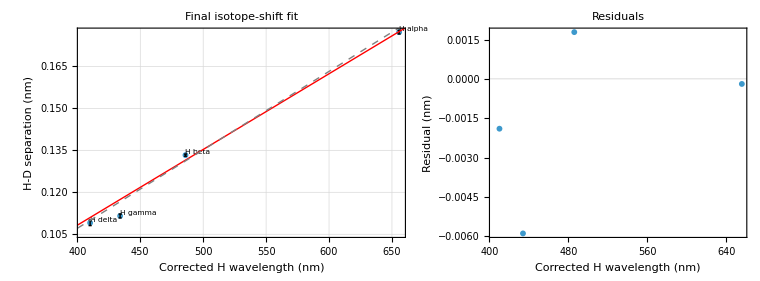

```mathematica
ClearAll["Global`*"];

(* ===============================================*)
(*Compact horizontal final isotope-shift figure*)
(* ===============================================*)

phase1Dir="C:\\Users\\ansht\\Downloads\\ansh-exp25\\ansh-exp25\\PHASE1_real_wavelength_files";

inputFile=FileNameJoin[{phase1Dir,"PHASE6_final_physics_fit","tables_for_latex","final_physics_input_points.csv"}];

outRoot=FileNameJoin[{phase1Dir,"PHASE6B_final_physics_fit_corrected"}];
figDir=FileNameJoin[{outRoot,"figures"}];

If[!DirectoryQ[outRoot],CreateDirectory[outRoot]];
If[!DirectoryQ[figDir],CreateDirectory[figDir]];

font="Arial";

toNum[x_]:=Module[{s},s=StringTrim[ToString[x]];
Quiet@Check[N@ToExpression[s],Missing["NA"]]];

raw=Import[inputFile,"CSV"];
headers=ToString/@First[raw];
records=AssociationThread[headers->#]&/@Rest[raw];

rows=records/. r_Association:><|"label"->ToString[r["label"]],"lambdaH"->toNum[r["lambdaH_corr_nm"]],"delta"->toNum[r["delta_corr_nm"]],"sigma"->toNum[r["delta_corr_SE_nm"]]|>;

rows=SortBy[rows,#["lambdaH"]&];

xvals=rows[[All,"lambdaH"]];
yvals=rows[[All,"delta"]];
sigmas=rows[[All,"sigma"]];
labels=rows[[All,"label"]];

weights=1/sigmas^2;

(*Correct zero-intercept weighted slope*)
s0=Total[weights xvals yvals]/Total[weights xvals^2];

res0=yvals-s0 xvals;

(*Free-intercept check,shown as dashed gray line*)
data=Transpose[{xvals,yvals}];

freeFit=LinearModelFit[data,{1,x},x,Weights->weights];

xMin=Min[xvals]-10;
xMax=Max[xvals]+10;

cap=0.005 (Max[xvals]-Min[xvals]);

errorBars=Graphics[Table[{Thin,Line[{{xvals[[i]],yvals[[i]]-sigmas[[i]]},{xvals[[i]],yvals[[i]]+sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]-sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]-sigmas[[i]]}}],Line[{{xvals[[i]]-cap,yvals[[i]]+sigmas[[i]]},{xvals[[i]]+cap,yvals[[i]]+sigmas[[i]]}}]},{i,Length[xvals]}]];

labelGraphics=Graphics[Table[Text[Style[labels[[i]],7.5,FontFamily->font],{xvals[[i]],yvals[[i]]},{-1.1,-1.2}],{i,Length[xvals]}]];

fitPlot=Show[ListPlot[data,Frame->True,Axes->False,PlotMarkers->{Automatic,6},ImageSize->430,AspectRatio->0.58,FrameLabel->{"Corrected H wavelength (nm)","H-D separation (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Final isotope-shift fit",10,FontFamily->font],PlotRange->All,ImagePadding->{{48,8},{35,18}}],errorBars,labelGraphics,Plot[s0 x,{x,xMin,xMax},PlotStyle->{Red,Thick}],Plot[freeFit[x],{x,xMin,xMax},PlotStyle->{Gray,Dashed,Thick}]];

residPlot=ListPlot[Transpose[{xvals,res0}],Frame->True,Axes->False,PlotMarkers->{Automatic,6},ImageSize->330,AspectRatio->0.58,FrameLabel->{"Corrected H wavelength (nm)","Residual (nm)"},LabelStyle->Directive[FontFamily->font,8],BaseStyle->{FontFamily->font},PlotLabel->Style["Residuals",10,FontFamily->font],GridLines->{None,{0}},PlotRange->All,ImagePadding->{{48,8},{35,18}}];

horizontalFig=GraphicsRow[{fitPlot,residPlot},Spacings->0.18,ImageSize->760];

outFile=FileNameJoin[{figDir,"corrected_final_isotope_shift_fit_and_residuals_horizontal_narrow.pdf"}];

Export[outFile,horizontalFig,"PDF"];

Print["Saved horizontal figure:"];
Print[outFile];

horizontalFig

SystemOpen[figDir];
```